# Inverse Statistics

Here, there are 3 functions that calculates minimum waiting for increase time by value h, and minimum waiting for decrease. 
The third function calculates the statistical properties of those said timeseries.

```mathematica
findMinimumTime[timeseries_,h_]:=Module[{n,result,len},n=Length[timeseries];
result=Table[Module[{j=i+1,minTime=Infinity},While[j<=n&&timeseries[[j]]<timeseries[[i]]+h,j++];
If[j<=n,j-i,Infinity]],{i,1,n}];
result]
```

```mathematica
findMinimumTimeDecrease[timeseries_,h_]:=Module[{n,result,len},n=Length[timeseries];
result=Table[Module[{j=i+1,minTime=Infinity},While[j<=n&&timeseries[[j]]>timeseries[[i]]-h,j++];
If[j<=n,j-i,Infinity]],{i,1,n}];
result]
```

```mathematica
inverseStatistics[timeseries_,h_,dt_]:=Module[{increments,time,steps=Length[timeseries]-1,plotGraph,plotIncrements,minTimes,incPlot,minTimesDecrease,decPlot,distMinTimes,distMinTimesDecrease,pdfMinTimes,pdfMinTimesDecrease,compare,histDec,histInc,smoothDistMinTimes,smoothDistMinTimesDecrease,cleanMinTimes,cleanMinTimesDecrease},
increments=Differences[timeseries]/dt;
time=Table[i*dt,{i,0,steps}];
plotGraph=ListLinePlot[Transpose[{time,timeseries}],PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","x(t)"},GridLines->Automatic,PlotLabel->"Stochastic Process"];
plotIncrements=ListLinePlot[Table[{time[[i]],increments[[i]]},{i,Length[increments]}],PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","dx/dt"},GridLines->Automatic,PlotLabel->"Time Derivative of the Stochastic Process (Increments)"];
minTimes=findMinimumTime[timeseries,h];
incPlot=ListLinePlot[Transpose[{Range[Length[timeseries]],minTimes}],PlotRange->All,PlotStyle->Thick,AxesLabel->{"Time Index","Minimum Time to Increase by h"},GridLines->Automatic,PlotLabel->"Minimum Waiting Time for Increase by "<>ToString[h]];
minTimesDecrease=findMinimumTimeDecrease[timeseries,h];
decPlot=ListLinePlot[Transpose[{Range[Length[timeseries]],minTimesDecrease}],PlotRange->All,PlotStyle->Thick,AxesLabel->{"Time Index","Minimum Time to Decrease by h"},GridLines->Automatic,PlotLabel->"Minimum Waiting Time for Decrease by "<>ToString[h]];
distMinTimes=EmpiricalDistribution[minTimes->1/Length[minTimes]];
distMinTimesDecrease=EmpiricalDistribution[minTimesDecrease->1/Length[minTimesDecrease]];
histInc=Histogram[minTimes,{1},"Probability",PlotLabel->"Histogram of minTimes",AxesLabel->{"Waiting Time","Probability"}];
histDec=Histogram[minTimesDecrease,{1},"Probability",PlotLabel->"Histogram of minTimesDecrease",AxesLabel->{"Waiting Time","Probability"}];
cleanMinTimes=Select[minTimes,#=!=∞&];
cleanMinTimesDecrease=Select[minTimesDecrease,#=!=∞&];
smoothDistMinTimes=SmoothKernelDistribution[cleanMinTimes];smoothDistMinTimesDecrease=SmoothKernelDistribution[cleanMinTimesDecrease];
compare=Plot[{PDF[smoothDistMinTimes,x],PDF[smoothDistMinTimesDecrease,x]},{x,Min[Join[cleanMinTimes,cleanMinTimesDecrease]]-1,Max[Join[cleanMinTimes,cleanMinTimesDecrease]]+1},PlotStyle->{Blue,Red},PlotLegends->{"minTimes","minTimesDecrease"},AxesLabel->{"Waiting Time","PDF"},PlotLabel->"Smoothed PDFs of Waiting Times (Without Infinity)"];
{plotGraph,plotIncrements,incPlot,decPlot,histInc,histDec,compare,smoothDistMinTimes,smoothDistMinTimesDecrease}
]
```

## Reading File

This  part reads the file, from the same directory of your mathematica notebook. change the name as you desire. I used gold data from a long time ago till now. Time resolution of this data is 1m.

```mathematica
notebookDirectory=NotebookDirectory[];
fileName="Gold.txt";
filePath=FileNameJoin[{notebookDirectory,fileName}];
timeSeries=Import[filePath,"CSV"][[All,1]]; 
timeSeries[[1;;10]]
```

{415.395,415.395,415.12,415.195,415.395,415.192,415.131,415.135,415.129,414.64}

This  part samples the data once every 60 data points (~1h), you can do this analysis on evert resolution you desire.

```mathematica
sampled=timeSeries[[Range[1,Length[timeSeries],60]]]
```

Here is a simple implementation of the code. first, you should input your data, then h value (here i chose 10 dollars) and then your desired time report. here i chose 1 hour, meaning the x axis is in terms of hours. 
the first figure is the data, the second it the derivative, third and fourth are for waiting time as in actual timeseries. the next two are histograms and the final one is reporting the PDF of said waiting times.

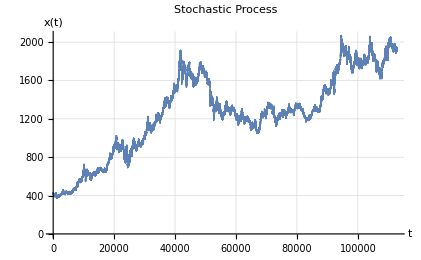
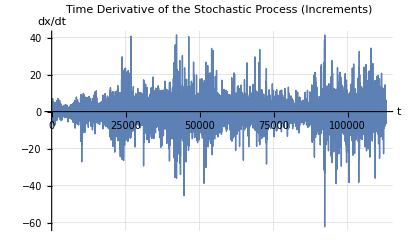
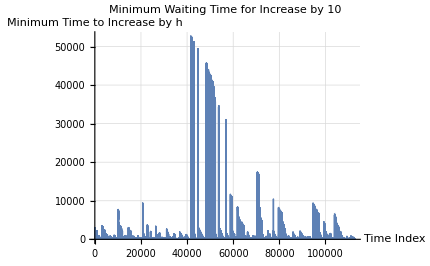
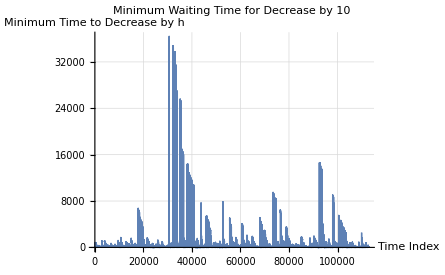
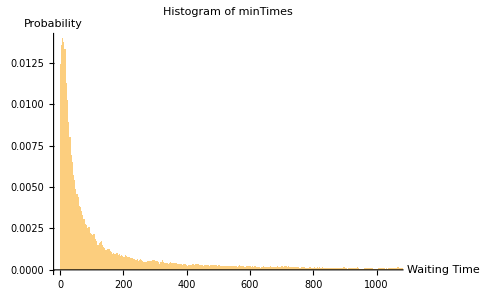
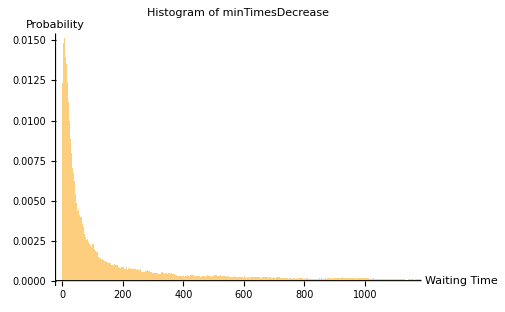
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
h=10;
inverseStatistics[sampled,h,1]
```

## Calculating for different h values

Change  randomwalk to your desired timeseries

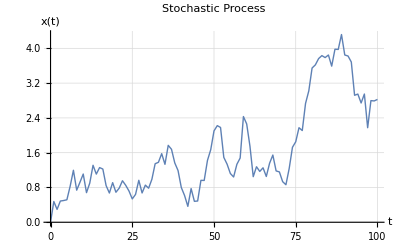
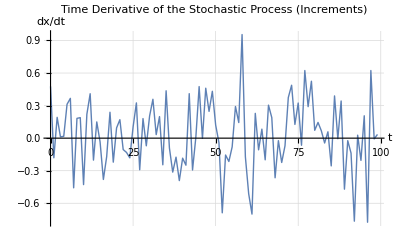
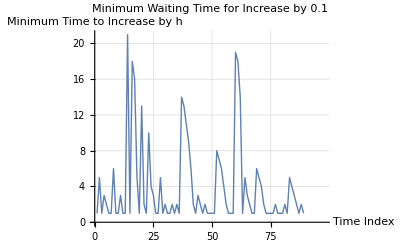
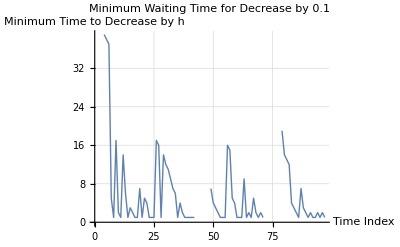
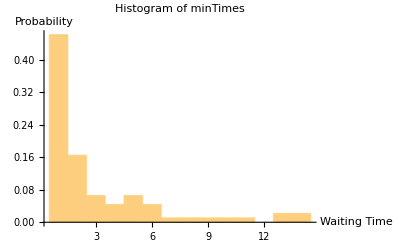
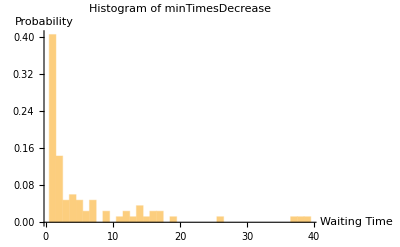
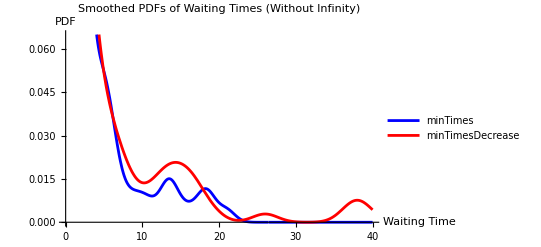
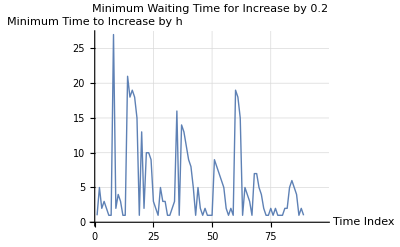
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
inverseStatistics[randomWalk,#,1]&/@{0.1,0.2,0.3}
```

## Parallel Computation

Here  i  have  used  the  parallel  method  that  uses  all  cpu  cores  to  calculate  the  desired timesries. feel free to change saving directory, h values and etc. all figures are saved, plus 2 reported WDX files for each of the PDFs.

```mathematica
hValues=Range[1,10,0.5];
outputDir=FileNameJoin[{NotebookDirectory[],"Results"}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];

ParallelTable[Module[{result,graphFiles,distFile1,distFile2,outputBase},result=inverseStatistics[(*put you timeseries here!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*),h,1];
graphFiles=Table[Export[FileNameJoin[{outputDir,"Graph_h_"<>ToString[h]<>"_Fig"<>ToString[i]<>".png"}],result[[i]]],{i,1,7}];
distFile1=FileNameJoin[{outputDir,"Distribution1_h_"<>ToString[h]<>".wdx"}];
distFile2=FileNameJoin[{outputDir,"Distribution2_h_"<>ToString[h]<>".wdx"}];
Export[distFile1,result[[8]]];
Export[distFile2,result[[9]]];
Print["Computed for h = ",h,", saved graphs to ",graphFiles,", saved distributions to ",{distFile1,distFile2}];
result],{h,hValues}];
```